# Physisorption Potential Function

```mathematica
?Table
```

Table[expr,{i_max}] generates a list of i_max copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
data= {{2.40*10^-10,9.443},{2.47*10^-10,5.383},{2.52*10^-10,3.234},{2.58*10^-10,1.483},{2.64*10^-10,-0.348},{2.72*10^-10,-1.781},{2.80*10^-10,-2.975},{2.91*10^-10,-4.09},{3.05*10^-10,-4.886},{3.30*10^-10,-5.204},{3.57*10^-10,-4.726},{3.86*10^-10,-4.09},{4.12*10^-10,-3.453},{4.45*10^-10,-2.816},{4.74*10^-10,-2.338},{5.01*10^-10,-2.02},{5.22*10^-10,-1.861},{5.40*10^-10,-1.622},{5.65*10^-10,-1.463},{5.85*10^-10,-1.303}}
```

(2.4×10^-10 | 9.443
2.47×10^-10 | 5.383
2.52×10^-10 | 3.234
2.58×10^-10 | 1.483
2.64×10^-10 | -0.348
2.72×10^-10 | -1.781
2.8×10^-10 | -2.975
2.91×10^-10 | -4.09
3.05×10^-10 | -4.886
3.3×10^-10 | -5.204
3.57×10^-10 | -4.726
3.86×10^-10 | -4.09
4.12×10^-10 | -3.453
4.45×10^-10 | -2.816
4.74×10^-10 | -2.338
5.01×10^-10 | -2.02
5.22×10^-10 | -1.861
5.4×10^-10 | -1.622
5.65×10^-10 | -1.463
5.85×10^-10 | -1.303)

```mathematica
fit= FindFormula[data,x,5]
```

FindFormula((2.4×10^-10 | 9.443
2.47×10^-10 | 5.383
2.52×10^-10 | 3.234
2.58×10^-10 | 1.483
2.64×10^-10 | -0.348
2.72×10^-10 | -1.781
2.8×10^-10 | -2.975
2.91×10^-10 | -4.09
3.05×10^-10 | -4.886
3.3×10^-10 | -5.204
3.57×10^-10 | -4.726
3.86×10^-10 | -4.09
4.12×10^-10 | -3.453
4.45×10^-10 | -2.816
4.74×10^-10 | -2.338
5.01×10^-10 | -2.02
5.22×10^-10 | -1.861
5.4×10^-10 | -1.622
5.65×10^-10 | -1.463
5.85×10^-10 | -1.303),x,5)

```mathematica
func = Interpolation[data]
```

-10         -10
InterpolatingFunction[{{2.4 10   , 5.85 10   }}, <>]

InterpolatingFunction::dmval: Input value TraditionalForm`{1.19507×10^-14} lies outside the range of data in the interpolating function. Extrapolation will be used.

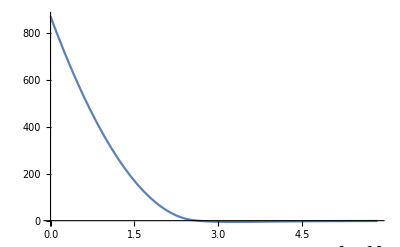

```mathematica
Plot[func[x],{x,0,5.85*10^-10}]
```

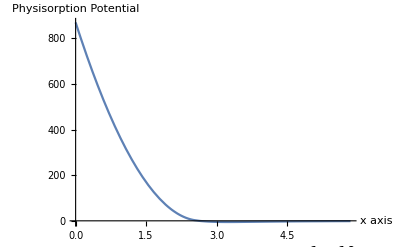

```mathematica
Show[%17,AxesLabel->{HoldForm[x axis],HoldForm[Physisorption Potential]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
fit= FindFormula[data ]
```

FindFormula((2.4×10^-10 | 9.443
2.47×10^-10 | 5.383
2.52×10^-10 | 3.234
2.58×10^-10 | 1.483
2.64×10^-10 | -0.348
2.72×10^-10 | -1.781
2.8×10^-10 | -2.975
2.91×10^-10 | -4.09
3.05×10^-10 | -4.886
3.3×10^-10 | -5.204
3.57×10^-10 | -4.726
3.86×10^-10 | -4.09
4.12×10^-10 | -3.453
4.45×10^-10 | -2.816
4.74×10^-10 | -2.338
5.01×10^-10 | -2.02
5.22×10^-10 | -1.861
5.4×10^-10 | -1.622
5.65×10^-10 | -1.463
5.85×10^-10 | -1.303))

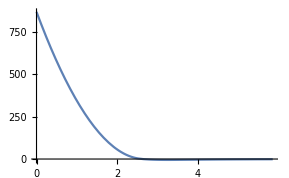
GetPolynomial(-Graphics-)

```mathematica
GetPolynomial[%17]
```

```mathematica
func // FullForm
```

InterpolatingFunction[List[List[2.4×10^-10,5.85×10^-10]],List[4,7,0,List[20],List[4],0,0,0,0,Automatic,List[],List[],False],List[List[2.4×10^-10,2.47×10^-10,2.52×10^-10,2.58×10^-10,2.64×10^-10,2.72×10^-10,2.8×10^-10,2.91×10^-10,3.05×10^-10,3.3×10^-10,3.57×10^-10,3.86×10^-10,4.12×10^-10,4.45×10^-10,4.74×10^-10,5.01×10^-10,5.22×10^-10,5.4×10^-10,5.65×10^-10,5.85×10^-10]],List[Developer`PackedArrayForm,List[0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20],List[9.443,5.383,3.234,1.483,-0.348,-1.781,-2.975,-4.09,-4.886,-5.204,-4.726,-4.09,-3.453,-2.816,-2.338,-2.02,-1.861,-1.622,-1.463,-1.303]],List[Automatic]]

```mathematica
NonlinearModelFit[data,a*x^3+b*x^2+c*x+d,{a,b,c,d},x]
```

FittedModel[-2.30407×10^30 x^3+«23» x^2«1»«22»«1»«1»+176.037]

```mathematica
%33["BestFit"]
```

-2.30407×10^30 x^3+3.06803×10^21 x^2-1.31203×10^12 x+176.037

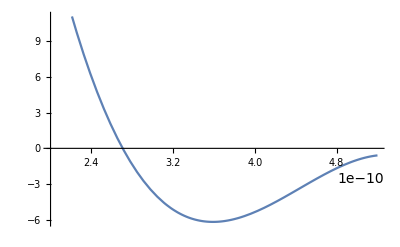

```mathematica
Plot[%34,{x,2*10^-10,5.2*10^-10}]
```

```mathematica
NonlinearModelFit[data,a/x^12-b/x^6,{a,b},x]
```

FittedModel[(1.22319×10^-114)/x^12-(«23»)/x^6]

```mathematica
%["BestFit"]
```

(1.22319×10^-114)/x^12-(4.21315×10^-57)/x^6

```mathematica
-D[(1.2231879883457419*^-114)/x^12-(4.213154864274522*^-57)/x^6, x]
```

(1.46783×10^-113)/x^13-(2.52789×10^-56)/x^7

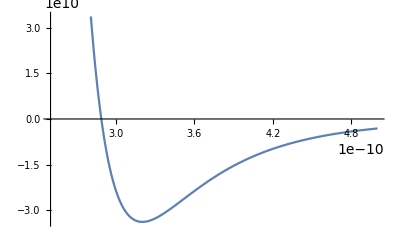

```mathematica
Plot[(1.46782558601489*^-113)/x^13-(2.527892918564713*^-56)/x^7,{x,2.5*10^-10,5*10^-10}]
```